# Thesis Notebook

## 2D Orbit with the improved Tolman VII neutron star density profile and mass function, along with dissipative forces

```mathematica
(*1. GLOBAL CONFIGURATION*)Needs["MaTeX`"];
exportDirectory="/home/em/Documents/thesis/neutron_star";
If[!FileExistsQ[exportDirectory],CreateDirectory[exportDirectory]];

(*Global Styling Variables*)
$ThesisFontSize=20;
$ThesisTickSize=14;
$ThesisImageSize=450; (*Slightly larger as requested*)
$ThesisThickness=2.0;
$GridStyle=Directive[GrayLevel[0.9],AbsoluteThickness[0.5]];
$FrameStyle=Directive[Black,AbsoluteThickness[1.2]];

(*REVERTED TO ORIGINAL COLORS*)
$ThesisColors={Blue,Red,Green,Purple,Darker[Green]};

SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath, amsfonts, amssymb, amsthm, bm, lmodern}","\\newcommand{\\rb}{\\bar{r}}","\\providecommand{\\e}[1]{\\ensuremath{\\times 10^{#1}}}"}];

ThesisStandardPlot[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f(\\rb)",xLabel_:"\\rb",labels_List:{},xTick_:None,pPoints_:1000,wPrec_:40,customStyles_:{}]:=Module[{finalPlot,plotOptions,fullPath,ticks,grid,usedStyles},ticks={Automatic,Automatic};
grid=Automatic;
(*Logic for specific xTick (r0)*)If[xTick=!=None,ticks={{Automatic,Automatic},{Union[FindDivisions[{vMin,vMax},6],{{xTick,MaTeX["\\bar{r}_0",FontSize->$ThesisFontSize]}}],Automatic}};
grid={{xTick},Automatic};];
(*Determine Styles:Use custom list if provided,else use default ThesisColors*)usedStyles=If[customStyles==={},Table[{$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],customStyles];
plotOptions={Exclusions-> None, Frame->True,Axes->False,PlotStyle->usedStyles,FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->Scaled[0.04],PlotPoints->pPoints,MaxRecursion->6,WorkingPrecision->wPrec,Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize-4,FontFamily->"Latin Modern Roman"}],{0.8,0.75}]],Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Standard (High-Precision): ",Green,Bold],fullPath];
finalPlot]

ThesisStandardPlotPOL[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f(\\rb)",xLabel_:"\\rb",labels_List:{},xTick_:None,pPoints_:100,wPrec_:30,customStyles_:{}]:=Module[{finalPlot,plotOptions,fullPath,ticks,grid,usedStyles},ticks={Automatic,Automatic};
grid=Automatic;
(*Logic for specific xTick (r0)*)If[xTick=!=None,ticks={{Automatic,Automatic},{Union[FindDivisions[{vMin,vMax},6],{{xTick,MaTeX["\\bar{r}_0",FontSize->$ThesisFontSize]}}],Automatic}};
grid={{xTick},Automatic};];
(*Determine Styles:Use custom list if provided,else use default ThesisColors*)usedStyles=If[customStyles==={},Table[{If[i==2,Directive[$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],Opacity[0.75]],$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],customStyles];
plotOptions={Frame->True,Axes->False,PlotStyle->usedStyles,FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->Scaled[0.04],PlotPoints->pPoints,MaxRecursion->6,WorkingPrecision->wPrec,Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize-4,FontFamily->"Latin Modern Roman"}],{0.8,0.75}]],Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Standard (High-Precision): ",Green,Bold],fullPath];
finalPlot]

(*2b.TIME PLOT FUNCTION-Font Matched to Standard Plot*)(*2b.TIME PLOT FUNCTION-Forced Ticks and Matched Fonts*)(*2b.TIME PLOT FUNCTION-Forced Ticks,Matched Fonts,2-Digit Precision*)ThesisStandardPlotTime[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f(\\bar{r})",xLabel_:"\\bar{r}",labels_List:{},xTick_:None]:=Module[{finalPlot,plotOptions,fullPath,ticks,grid,xDivs,proximityThreshold,numFuncs,currentColors},numFuncs=Length[Flatten[{funcs}]];
currentColors=Table[$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],{i,numFuncs}];
ticks={Automatic,Automatic};
grid={Automatic,Automatic};
If[xTick=!=None,xDivs=FindDivisions[{vMin,vMax},6];
proximityThreshold=(vMax-vMin)*0.08;
ticks={{Automatic,Automatic},{Union[Select[xDivs,Abs[#-xTick]>proximityThreshold&],{{xTick,MaTeX["t_{\\text{s}}",FontSize->$ThesisFontSize]}}],None}};];
plotOptions={Frame->True,Axes->False,PlotStyle->Table[{currentColors[[i]],AbsoluteThickness[$ThesisThickness]},{i,numFuncs}],FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->{Scaled[0.02],Scaled[0.1]},Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[currentColors,MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize,FontFamily->"Latin Modern Roman"}],{0.8,0.75}]],Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Time Plot: ",Green,Bold],fullPath];
finalPlot]

ThesisStandardPlotRadial[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"\\bar{r}(t)",xLabel_:"t",labels_List:{},rbarStar_:None]:=Module[{finalPlot,plotOptions,fullPath,numFuncs,currentColors,shading},numFuncs=Length[Flatten[{funcs}]];
currentColors=Table[$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],{i,numFuncs}];
(*Shading logic:Rectangle from y=0 to y=rbarStar across the full x-range*)shading=If[rbarStar===None,{},{Directive[Cyan,Opacity[0.5]],Rectangle[{vMin,0},{vMax,rbarStar}]}];
plotOptions={Frame->True,Axes->False,Prolog->shading,PlotStyle->Table[{currentColors[[i]],AbsoluteThickness[$ThesisThickness]},{i,numFuncs}],FrameStyle->$FrameStyle,FrameTicks->{Automatic,Automatic},FrameTicksStyle->Directive[Black,$ThesisTickSize],(*Updated to use your global grid variables for uniformity*)GridLines->{Automatic,Automatic},GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->{Automatic,All},PlotRangePadding->{Scaled[0.02],Scaled[0.1]},Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[currentColors,MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize,FontFamily->"Latin Modern Roman"}],{0.75,0.75}]],Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Radial Plot: ",Green,Bold],fullPath];
finalPlot]

(*2c.PIECEWISE PLOT FUNCTION-Updated for Round Numbers*)
ThesisPiecewisePlot[func_,{var_,vMin_,vMax_},rStar_,fileName_String,yLabel_:"f(\\bar{r})",xLabel_:"\\bar{r}",labels_List:{},xTick_:None]:=Module[{finalPlot,plotOptions,fullPath,ticks,grid,xDivs,proximityThreshold},ticks={Automatic,Automatic};grid={Automatic,Automatic};
If[xTick=!=None,xDivs=FindDivisions[{vMin,vMax},6];
proximityThreshold=(vMax-vMin)*0.08;
ticks={{Automatic,Automatic},{Union[Select[xDivs,Abs[#-xTick]>proximityThreshold&],{{xTick,MaTeX["\\bar{R}_*",FontSize->$ThesisFontSize]}}],None}};];
plotOptions={Frame->True,Axes->False,ColorFunction->Function[{x,y},If[x<rStar,Blue,Red]],ColorFunctionScaling->False,PlotStyle->{AbsoluteThickness[$ThesisThickness+0.5]},FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->{Scaled[0.02],Scaled[0.1]},Exclusions->None,Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[func,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[{Blue,Red},MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize,FontFamily->"Latin Modern Roman"}],{0.2,0.75}]],Plot[func,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Piecewise: ",Green,Bold],fullPath];finalPlot]

(*3. MASTER ORBIT FUNCTION*)
ThesisOrbitPlot[{xFunc_,yFunc_},{var_,vMin_,vMax_},rStar_,fileName_String,xLabel_:"\\bar{r}(t)\\cos(\\phi(t))",yLabel_:"\\bar{r}(t)\\sin(\\phi(t))",xTick_:None]:=Module[{orbitLine,body,finalPlot,fullPath,ticks,extras,startPos,plotBoundaries,xDivs,xRangeWidth},orbitLine=ParametricPlot[{xFunc,yFunc},{var,vMin,vMax},PlotStyle->{Darker[Blue],AbsoluteThickness[1.5]},PlotPoints->300];
body=Graphics[{Cyan,EdgeForm[{Cyan,AbsoluteThickness[1]}],Disk[{0,0},rStar]}];
ticks={Automatic,Automatic};extras={};
If[xTick=!=None,startPos={xFunc,yFunc}/. var->vMin;
extras={Directive[GrayLevel[0.4],Dashed,AbsoluteThickness[1]],InfiniteLine[{xTick,0},{0,1}],Directive[Black],Disk[startPos,Offset[3]]};
plotBoundaries=PlotRange/. AbsoluteOptions[orbitLine,PlotRange];
xRangeWidth=Abs[plotBoundaries[[1,2]]-plotBoundaries[[1,1]]];
xDivs=FindDivisions[plotBoundaries[[1]],6];
xDivs=Select[xDivs,Abs[#-xTick]>0.10*xRangeWidth&];
ticks={{Automatic,Automatic},{Union[Table[{i,i},{i,xDivs}],{{xTick,MaTeX["\\rb_0",FontSize->$ThesisFontSize]}}],Automatic}};];
finalPlot=Show[body,Graphics[extras],orbitLine,Frame->True,Axes->False,AspectRatio->Automatic,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->Automatic,GridLinesStyle->$GridStyle,ImageSize->$ThesisImageSize,PlotRange->All,PlotRangePadding->Scaled[0.08]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Orbit: ",Blue,Bold],fullPath];finalPlot]

(*4. LOGARITHMIC PLOTTING FUNCTION*)
ThesisLogPlot[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f",xLabel_:"t",tSurface_:None]:=Module[{finalPlot,fullPath,ticks,grid},grid={If[NumberQ[tSurface],{tSurface},{}],Automatic};
ticks={Automatic,{Join[FindDivisions[{vMin,vMax},6],If[NumberQ[tSurface],{{tSurface,MaTeX["t_{\\text{s}}",FontSize->$ThesisFontSize]}},{}]],Automatic}};
finalPlot=LogPlot[funcs,{var,vMin,vMax},Frame->True,Axes->False,PlotStyle->Table[{$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->{{vMin,vMax},All},PlotRangePadding->{None,Scaled[0.05]},Method->{"DefaultBoundaryStyle"->None}];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Log Plot: ",Magenta,Bold],fullPath];finalPlot]

ThesisStandardLogLogPlot[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"m(t)",xLabel_:"t",labels_List:{}]:=Module[{finalPlot,fullPath,startPoint,legendColors},(*1. Setup scale start point*)startPoint=If[vMin==0,10^-3,vMin];
(*2. Prepare colors for the legend based on the number of functions*)legendColors=Table[$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],{i,Length[Flatten[{funcs}]]}];
finalPlot=LogLogPlot[funcs,{var,startPoint,vMax},(*Visuals*)Frame->True,Axes->False,FrameStyle->$FrameStyle,FrameTicksStyle->Directive[Black,$ThesisTickSize],FrameTicks->{{Automatic,None},{Automatic,None}},GridLines->{Automatic,Automatic},GridLinesStyle->$GridStyle,(*Labels& Sizing*)FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,(*Line Style*)PlotStyle->Table[{legendColors[[i]],AbsoluteThickness[$ThesisThickness]},{i,Length[legendColors]}],(*Legend Formatting-Matched to Piecewise Function*)PlotLegends->If[Length[labels]>0,Placed[LineLegend[legendColors,MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize,FontFamily->"Latin Modern Roman"}],{0.8,0.8}],(*Position:Top Right for Log-Log usually works best*)None],PlotRange->Automatic];
(*Export logic*)fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Matched Log-Log: ",Black,Bold],fullPath];
finalPlot]

ThesisListPlot[data_,fileName_String,yLabel_:"Power",xLabel_:"Frequency (Hz)"]:=Module[{finalPlot,fullPath},finalPlot=ListLinePlot[data,Frame->True,Axes->False,PlotStyle->{Red,AbsoluteThickness[$ThesisThickness]},FrameStyle->$FrameStyle,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->Automatic,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->{{0, 10000}, All},PlotRangePadding->Scaled[0.02]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Linear Spectrum: ",Red,Bold],fullPath];
finalPlot]

ThesisLogLogPlot[data_,fileName_String,yLabel_:"Power",xLabel_:"Frequency (Hz)"]:=Module[{finalPlot,fullPath},finalPlot=ListLogLogPlot[data,Frame->True,Axes->False,PlotStyle->{Red,AbsoluteThickness[$ThesisThickness]},FrameStyle->$FrameStyle,FrameTicksStyle->Directive[Black,$ThesisTickSize],(*Specific log grid behavior*)GridLines->Automatic,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,(*Adjusting PlotRange:Log plots cannot start at 0*)PlotRange->All,PlotRangePadding->Scaled[0.02]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Log-Log Spectrum: ",Red,Bold],fullPath];
finalPlot]

ThesisListPlotPeak[data_,fileName_String,yLabel_:"Power",xLabel_:"Frequency (Hz)",pRange_:All]:=Module[{finalPlot,fullPath,peakFreq,peakPower,extras,ticks,xDivs,xRangeWidth},(*1. Find the Peak Automatically*)(*data is assumed to be a list of {freq,power}*){peakFreq,peakPower}=First@SortBy[data,Last][[-1]];
(*2. Create the vertical dashed line and a dot at the peak*)extras={Directive[GrayLevel[0.4],Dashed,AbsoluteThickness[1]],InfiniteLine[{peakFreq,0},{0,1}],Directive[Red],PointSize[Medium],Point[{peakFreq,peakPower}]};
(*3. Logic for Ticks (Handling the start at 10 and labeling the peak)*)(*If pRange is All,we use the data limits;otherwise use pRange limits*){vMin,vMax}=If[pRange===All,{Min[data[[All,1]]],Max[data[[All,1]]]},pRange[[1]]];
xRangeWidth=vMax-vMin;
xDivs=FindDivisions[{vMin,vMax},6];
(*Filter out auto-ticks too close to the peak label*)xDivs=Select[xDivs,Abs[#-peakFreq]>0.10*xRangeWidth&];
ticks={{Automatic,Automatic},{Union[xDivs,{{peakFreq,MaTeX[ToString[Round[peakFreq,0.1]]<>"\\text{ Hz}",FontSize->$ThesisFontSize]}}],Automatic}};
finalPlot=ListLinePlot[data,Frame->True,Axes->False,PlotStyle->{Red,AbsoluteThickness[$ThesisThickness]},FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->{{peakFreq},Automatic},GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->pRange,PlotRangePadding->{None,Scaled[0.1]},Epilog->extras (*Adds the dashed line*)];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Peak Found at: ",Bold],peakFreq," Hz"];
finalPlot]
```

## Setting functions up and choosing variables

## Star constants

```mathematica
(*From wikipedia paper*)
```

```mathematica
Msol = 1.989 10^30;
G = 6.6743 10^-11;
c = 3 10^8;
```

```mathematica
Mdummy = (G 1.4Msol)/c^2
```

2065.03

```mathematica
Rdummy = (12 10^3)/Mdummy;
```

```mathematica
infprec[lowlyprecision_, p_] := 10^-p Round[(10^p) lowlyprecision]
R = infprec[Rdummy, 10];
```

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = R;(*Radius of the Star*)
M = 1;
R // N
```

5.81106

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄), r̄(r)

```mathematica
rbarofrOutside[r_] := 1/2 (-M + r + Sqrt[r^2 - 2 M r]);
```

```mathematica
rbarStar = rbarofrOutside[RStar];
```

```mathematica
rofrbarOutside[rbar_] :=rbar (1 + M/(2 rbar))^2;
```

### A(r̄), α(r̄)

```mathematica
A[rbar_] :=(1 + M/(2 rbar))^2;
α[rbar_] :=(1 - M/(2 rbar))/(1 + M/(2 rbar));
```

## Tolman VII improved Isotropic coords definitions

### Constants

```mathematica
ScriptC = M/RStar;
Precision[ScriptC]
```

∞

### Universal alpha factor

```mathematica
infprec[lowlyprecision_, p_] := 10^-p Round[(10^p) lowlyprecision]
```

```mathematica
a1 = infprec[3.70625, 2];
a2 = infprec[1.50266, 2];
a3 = infprec[0.0643875,2];
n = infprec[.903, 2];

Precision[{a1, a2, a3, n}]
```

∞

```mathematica
alphaaaFunc[a1_, a2_, a3_, n_] :=a1 -a2(ScriptC^n/(rho0*RStar^2))+a3(ScriptC^n/(rho0*RStar^2))^2 ;
```

```mathematica
alphaaa= alphaaaFunc[a1, a2, a3, n];
Precision[alphaaa]
```

∞

```mathematica
(*alphadummy = infprec[alphaadummy, 60];*)
```

```mathematica
(*alphaaa = SetPrecision[alphadummy, 60];*)
```

### New interior rho

```mathematica
Clear[rho0]
rhoInside[r_] := rho0(1 - alphaaa (r/RStar)^2 + (alphaaa-1)(r/RStar)^4)
```

```mathematica
massIntegral =  4 Pi Integrate[rhoInside[r] r^2, {r, 0, RStar}];
```

```mathematica
N[%]
```

12.5664 (0.102207-0.0000248427/rho0-4.22362 rho0)

```mathematica
sol = Solve[massIntegral == 1, rho0];
(*Larger density seems more realistic for neutron star*)
```

```mathematica
N[%]
```

{{rho0→0.00154111},{rho0→0.00381664}}

```mathematica
rho0 = rho0 /. sol[[2]];
```

```mathematica
N[%]
```

0.00381664

```mathematica
Precision[rho0]
```

∞

```mathematica
massIntegral =  4 Pi Integrate[rhoInside[r] r^2, {r, 0, RStar}]
```

1

### New mass function

```mathematica
MassFuncInside[r_] := 4 Pi rho0 RStar^3 ( 1/3(r/RStar)^3 - alphaaa/5(r/RStar)^5 + ((alphaaa-1)/7)(r/RStar)^7)
```

## Numerically integrating for the pressure and the phi in α = exp(phi)

### Defining the ODEs

```mathematica
(*TOV differential equation*)
dPdr[r_, Pressure_] := -(rhoInside[r] + Pressure)((MassFuncInside[r] + 4 Pi Pressure r^3)/(r(r-2MassFuncInside[r])));
```

```mathematica
(*Phi differential equation for metric*)
dPhidrMetric[r_, Pressure_] := ((MassFuncInside[r] + 4 Pi Pressure r^3)/(r(r-2MassFuncInside[r])));
```

#### Numerically integrating these coupled ODEs

```mathematica
rmin = 10^-16;
```

```mathematica
eq1 = P'[r] == dPdr[r, P[r]];
eq2 = Phi'[r] == dPhidrMetric[r, P[r]];
BCs = {P[RStar] == 0, Phi[RStar] == 1/2 Log[1-2 M/RStar]} ;(*Phi[RStar] from the Schwarzschild metric*)
```

```mathematica
sol1 = NDSolve[
{eq1,
eq2,
BCs},
{P, Phi},
{r, RStar, rmin},
WorkingPrecision->55
][[1]]; (*Very small rmin to avoid singularity sarp mentioned*)
```

```mathematica
eq1[[2]]//Precision
```

∞

```mathematica
Pressure[r_] := P[r] /. sol1

PhiMetric[r_] = Phi[r] /. sol1;
```

## Solving for r̄(r) and r(r̄) inside

### Defining the ODE

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFuncInside[r])/r)^(-1/2)
```

### Numerically Integrating the above equation

```mathematica
eq = rbarofr'[r] == drbardr[rbarofr[r], r];
BC = {rbarofr[RStar] == rbarStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rbarofr},
{r, RStar, rmin},
WorkingPrecision->55
][[1]];
```

```mathematica
rbarofrInside[r_] = rbarofr[r] /. sol2;
```

#### Some sanity checks

```mathematica
rbarofrInside[RStar]
rbarofrOutside[RStar] //N
```

4.7585207028157789763475275419317953926785017940593318

4.75852

### Now using the interpolation trick to obtain r(r̄): (causing issues?)

```mathematica
(*Table[ expression, {variable, start, end, step}*)
data = Table[
{rbarofrInside[r], r}, 
{r, rmin, RStar, (RStar - rmin)/10000} (*10000 points and A is not messy*)
];
```

```mathematica
rofrbarInside = Interpolation[data];
```

```mathematica
rofrbarFull[rbar_]:= Piecewise[
{
{rofrbarOutside[rbar], rbar>=rbarStar},
{rofrbarInside[rbar], rbar < rbarStar}
}
]
```

Saved Piecewise: /home/em/Documents/thesis/neutron_star/rofrbar.pdf

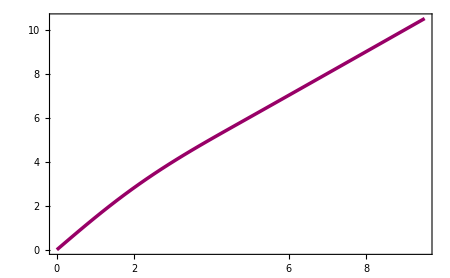

```mathematica
ThesisPiecewisePlot[rofrbarFull[r],{r,0,2*rbarStar},rbarStar,"rofrbar","r(\\bar{r})","\\bar{r}",{"\\large{\\textbf{Inside}}","\\large{\\textbf{Outside}}"},rbarStar]
```

## Finding the interior metric functions

### Getting αInside(r̄):

```mathematica
αInside[rbar_] := Exp[PhiMetric[rofrbarInside[rbar]]]
```

#### Sanity checks

```mathematica
αInside[rbarStar]
α[rbarStar] //N
```

0.8098324497487420349949376745265658247829504973959603242

0.809832

```mathematica
αFull[rbar_] := Piecewise[
{
{αInside[rbar], rbar < rbarStar},
{α[rbar], rbar >= rbarStar}
}
]
```

Saved Piecewise: /home/em/Documents/thesis/neutron_star/Alpha_Metric_Plot.pdf

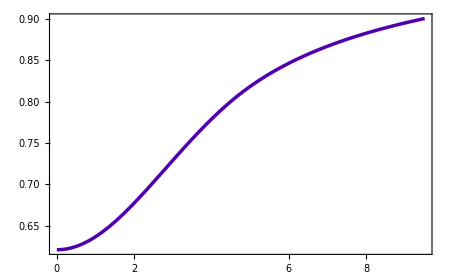

```mathematica
ThesisPiecewisePlot[αFull[r],{r,0,2rbarStar},rbarStar,"Alpha_Metric_Plot","\\alpha(\\bar{r})","\\bar{r}",{"\\large{\\textbf{Inside}}","\\large{\\textbf{Outside}}"},rbarStar]
```

```mathematica
PlotInside = Plot[αInside[rbar], {rbar, 0, rbarStar}];
PlotOutside = Plot[α[rbar], {rbar, rbarStar, 2*rbarStar}];
```

### Making the derivative of alpha continuous

#### Interior derivative in terms of r

Doing things in r first as this is more analytic

```mathematica
dPhidrMetric[r_] := ((MassFuncInside[r] + 4 Pi Pressure[r] r^3)/(r(r-2MassFuncInside[r])))
```

```mathematica
alpha[r_] := Exp[PhiMetric[r]]
DERalphaIns[r_] := dPhidrMetric[r] alpha[r] (*Something analytic times a numerical integral*)
```

#### Exterior derivative in terms of r

```mathematica
DERαOutsiderbardummy = Derivative[1][α][rbar];
DERαOutsiderbar[r_] := ((1-1/(2 rbar))/(2 (1+1/(2 rbar))^2 rbar^2)+1/(2 (1+1/(2 rbar)) rbar^2) )/. rbar -> rbarofrOutside[r] (*More accurate subbing in after for rbar maybe?*)
drbardr[r_] := rbarofrOutside[r]/r(1 - (2M)/r)^(-1/2)
```

```mathematica
DERalpha[r_] := drbardr[r]  DERαOutsiderbar[r] (*Chain rule*)
```

#### Sanity check at boundary

```mathematica
DERalpha[RStar] //N
DERalphaIns[RStar] //N
```

0.0365674

0.0365674

```mathematica
DERalphaIns[rofrbarInside[rbarStar]]
DERalpha[rofrbarInside[rbarStar]]
```

0.036567426666347078533901270803968692515330497513626698

0.036567426666347078533901270803968692515330497513626698

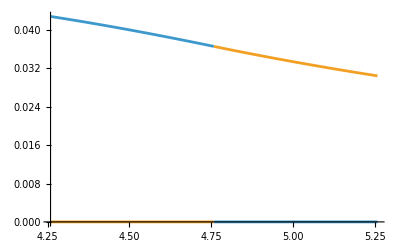

```mathematica
Plot[{Piecewise[{{DERalphaIns[rofrbarInside[rbar]],rbar<=rbarStar}}],Piecewise[{{DERalpha[rofrbarOutside[rbar]],rbar>=rbarStar}}]},{rbar,rbarStar-0.5,rbarStar+0.5}]
```

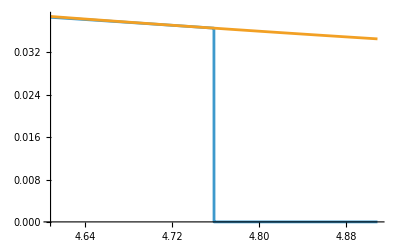

```mathematica
Plot[{DERalphaIns[rofrbarInside[rbar]],DERalpha[rofrbarOutside[rbar]]},{rbar,rbarStar-0.15,rbarStar+0.15}]
```

#### I messed up coordinate transforms here, that’s why the numbers were off.

```mathematica
(*DERalpha[rbarofrOutside[RStar]] //N (*Think I am making a mess of coordinate tranforms here as they are the same above and in the graph*)
DERalphaIns[rbarofrInside[RStar]] //N (*More or less continuous now but not exact*)*)
```

```mathematica
(*diff = Abs[1 - DERalphaIns[rbarofrInside[RStar]]/DERalpha[rbarofrOutside[RStar]]]*)
```

```mathematica
(*Abs[Log10[diff]] (*Amount of digits in agreement*)*)
```

### Isotropic coordinates DERα definitions

```mathematica
DERαOutside[rbar_] := Module[{r = rofrbarOutside[rbar]}, drbardr[r]  DERαOutsiderbar[r]]

DERαInside[rbar_] := Module[{r = rofrbarInside[rbar]},
dPhidrMetric[r] alpha[r]]
```

```mathematica
DERαFull[rbar_] := Piecewise[
{
{DERαInside[rbar], rbar < rbarStar},
{DERαOutside[rbar], rbar >= rbarStar}
}
]
```

#### Sanity checks

```mathematica
DERαInside[rbarStar]
```

0.036567426666347078533901270803968692515330497513626698

```mathematica
DERαOutside[rbarStar] //N
```

0.0365674

```mathematica
(*DERαFull[rbar_]:=If[rbar<rbarStar,DERαInside[rbar],DERαOutside[rbar]]*)
```

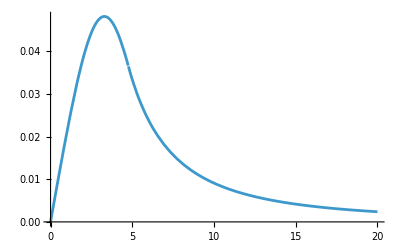

```mathematica
Plot[DERαFull[rbar], {rbar, 0, 20}]
```

### Getting AInside(r̄):

```mathematica
AInside[rbar_] := rofrbarInside[rbar]/rbar;
```

#### Sanity checks

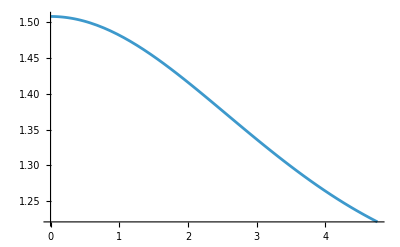

```mathematica
Plot[AInside[rbar], {rbar, 0, rbarStar}]
```

```mathematica
A[rbarStar] // N
AInside[rbarStar]
```

1.22119

1.22119002974210005813928324088936724178059425690799276

```mathematica
AFull[rbar_] := Piecewise[
{
{A[rbar], rbar >= rbarStar},
{AInside[rbar], rbar < rbarStar}
}
];
```

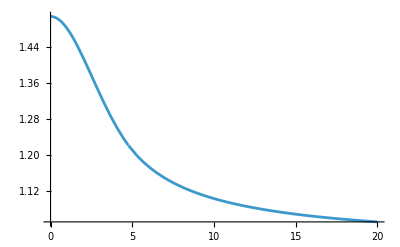

```mathematica
Plot[AFull[rbar], {rbar, 0, 20}]
```

### Isotropic coordinates definitions of DERA:

#### Inside

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFuncInside[r])/r)^(-1/2)
drdrbar[rbar_] := rofrbarInside[rbar]/rbar(1 - (2MassFuncInside[rofrbarInside[rbar]])/rofrbarInside[rbar])^(1/2)
```

```mathematica
(*Chain rule below from AInside*)
```

```mathematica
DERAInside[rbar_] := drdrbar[rbar]/rbar - rofrbarInside[rbar]/rbar^2;
```

#### Outside

```mathematica
DERAOutside[rbar_] := Derivative[1][A][rbar]
```

#### Full

```mathematica
DERAFull[rbar_] := Piecewise[
{
{DERAOutside[rbar], rbar >=rbarStar},
{DERAInside[rbar], rbar < rbarStar}
}
];
```

#### Sanity checks

```mathematica
DERAOutside[rbarStar] // N
DERAInside[rbarStar]
```

-0.0488031

-0.048803132496596513114854657172571746137910837350911849

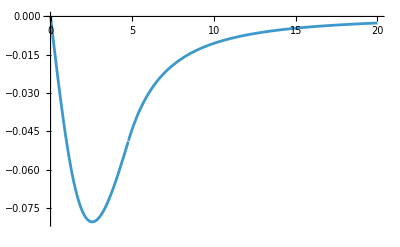

```mathematica
Plot[DERAFull[rbar], {rbar, 0, 20}]
```

### Defining the speed of sound a(r):

```mathematica
drhodr[r_]:= Derivative[1][rhoInside][r]
```

```mathematica
cutoffIso = .99999999999999rbarStar
```

4.75852

```mathematica
aFirst[rbar_] := Sqrt[dPdr[rofrbarInside[rbar],Pressure[rofrbarInside[rbar]]]/(drhodr[rofrbarInside[rbar]])]
```

```mathematica
aFirst[cutoffIso]
```

4.63215×10^-8

```mathematica
(*Needed to implement these measures to speed things up using Module to avoid recomputation and also the N@ to return numbers instead of symbols for NDSolve, pressure was causing an issue*)
(*Module avoids repeating the calculation three times as there were three arguments I would have had to have inputted it in*)
```

```mathematica
asosPiecewise[rbar_?NumericQ]:=Module[{r=rofrbarInside[rbar]},Piecewise[{
{Sqrt[dPdr[r,Pressure[r]]/drhodr[r]],rbar<cutoffIso},
{aFirst[cutoffIso], rbar >= cutoffIso}
}
]
]
```

```mathematica
(*asosPiecewise[rbar_?NumericQ]:=Module[{r=rofrbarInside[rbar]}, N@Sqrt[dPdr[r,Pressure[r]]/drhodr[r]]]*)
```

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_asos.pdf

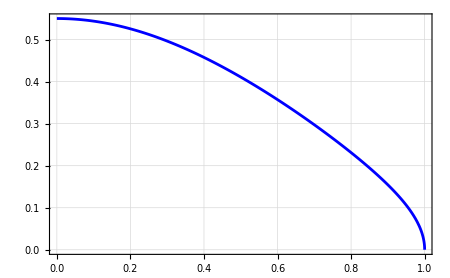

```mathematica
ThesisStandardPlot[asosPiecewise[x*rbarStar],(*1. The function (scaled back to rbar)*){x,0,1},(*2. Plotting from 0 to 1 on the x-axis*)"Fig_asos",(*3. Filename*)"a(\\bar{r})",(*4. y-label*)"\\bar{r}/\\bar{R}^*",(*5. x-label (The scaled label)*){},(*6. No legends*)None,(*7. No specific x-tick*)200,(*8. PlotPoints (Higher for Piecewise)*)30                                (*9. WorkingPrecision*)]
```

## Setting up 2D ODEs for new density profile:

```mathematica
Isorho[rbar_] := Module[{r = rofrbarInside[rbar]}, rho0(1 - alphaaa (r/RStar)^2 + (alphaaa-1)(r/RStar)^4)]
```

```mathematica
IsotropicCoordsPressure[rbar_] := Pressure[rofrbarInside[rbar]]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_pressure.pdf

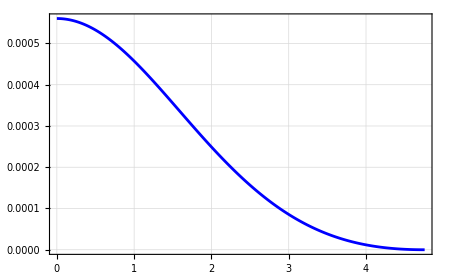

```mathematica
ThesisStandardPlot[IsotropicCoordsPressure[rbar],{rbar,0,rbarStar},"Fig_pressure","P(\\rb)","\\rb"]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_phi_metric.pdf

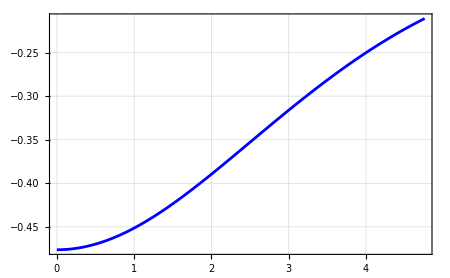

```mathematica
ThesisStandardPlot[PhiMetric[rofrbarInside[rbar]],{rbar,0,rbarStar},"Fig_phi_metric","\\Phi(\\rb)","\\rb"]
```

Constants that are going to be used

### Mach number interpolation

#### Interpolating

```mathematica
fMachLow[m_] := 1/2 Log[(1+ m)/(1 - m)] - m ;
fMachhigh[m_] := 1/2 Log[1 - 1/m^2]  + 10
```

```mathematica
x1=.9999;
x2=1.0001;
y1=fMachLow[x1];
y2=fMachhigh[x2];
```

```mathematica
anaylticline[Mach_] := y1 + (y2 - y1) (Mach - x1)/(x2 - x1)
```

```mathematica
IVariableInterpolated[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < x1},
{anaylticline[Μach], x1 <= Μach  < x2},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach >= x2}
}];
```

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_I_var_mach_interp.pdf

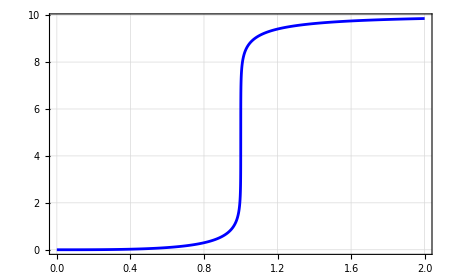

```mathematica
ThesisStandardPlot[IVariableInterpolated[Mach], {Mach, 0, 2},"Fig_I_var_mach_interp","I(\\mathcal{M})","\\mathcal{M}"]
```

### Outside Star

#### Velocities

```mathematica
Ut[rbar_, ur_, uphi_] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
umagOutside[rbar_, ur_, uphi_]:=(√(ur^2+(uphi/rbar)^2))/A[rbar]
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_, ur_, uphi_] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_,ur_, uphi_] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;
```

Gravitational Waves

```mathematica
FRRr[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarOutside[rbar]},((8 m^2)/(15 r^4)*drBardt[rbar, ur, uphi]*(8 M^2+r M (6 drBardt[rbar, ur, uphi]^2+36 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
FRRphi[m_, rbar_,ur_, uphi_]:= Module[{r = rofrbarOutside[rbar]},((8 m^2)/(5 r^4)*dphidtOutside[rbar,ur, uphi]*(2 M^2+r M (9 drBardt[rbar, ur, uphi]^2-6 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
duphidtOutside[m_, rbar_, ur_, uphi_] := η/m(A[rbar]^2 rbar^2 FRRphi[m, rbar, ur, uphi]);

durdt2DOutside[m_, rbar_, ur_, uphi_] := -α[rbar] Ut[rbar, ur, uphi] DERαOutside[rbar] + ur^2/Ut[rbar, ur, uphi](DERAOutside[rbar]/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + DERAOutside[rbar]/(rbar^2*A[rbar]^3)) + η/m(A[rbar]^2 FRRr[m, rbar, ur, uphi]);
```

### Inside Star

#### Velocities

```mathematica
UtInside[rbar_, ur_, uphi_] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagInside[rbar_, ur_, uphi_] := (√(ur^2+(uphi/rbar)^2))/AInside[rbar]
```

#### Mach business

```mathematica
Mach[rbar_, ur_, uphi_] :=umagInside[rbar, ur, uphi]/(asosPiecewise[rbar] αInside[rbar] UtInside[rbar, ur, uphi])
```

#### Dissipative Forces

Accretion

```mathematica
mdot[m_, rbar_, ur_, uphi_] := (4Pi Isorho[rbar] m^2)/((asosPiecewise[rbar]^2 + (umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)); (*General Bondi-Hoyle-Lyttleton formula for mass accretion with q = 3 and λ=1*)
```

```mathematica
dpdtaccretionr[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar](Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/((asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)))ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar](Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/((asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)))uphi
```

Drag

```mathematica
dpdtdragphi[m_, rbar_, ur_, uphi_] := 1/umagInside[rbar, ur, uphi]^3(-4π αInside[rbar]*(Isorho[rbar] + IsotropicCoordsPressure[rbar])*m^2*(1 + 2 umagInside[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);

dpdtdragr[m_, rbar_, ur_, uphi_] := (-4π αInside[rbar](Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2(1 + 2 umagInside[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagInside[rbar, ur, uphi]^3;
```

#### Rates of change of velocities

```mathematica
drBardtInside[rbar_, ur_, uphi_] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_, ur_, uphi_] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;
```

```mathematica
Mp[r_] := Derivative[1][MassFuncInside][r]
Mpp[r_] := Derivative[2][MassFuncInside][r]
Mppp[r_] := Derivative[3][MassFuncInside][r]
```

```mathematica
FRRrIns[m_, rbar_, ur_, uphi_]:= Module[{r = rofrbarInside[rbar]},(8 m^2)/(15 r^4)*drBardtInside[rbar, ur, uphi]*(8 MassFuncInside[r]^2+r MassFuncInside[r] (6 drBardtInside[rbar, ur, uphi]^2+36 r^2 dphidtInside[rbar, ur, uphi]^2+Mp[r]-3 r Mpp[r])-r^2 ( Mp[r]^2+3 r^2 dphidtInside[rbar, ur, uphi]^2 (6 Mp[r]-r Mpp[r])+drBardtInside[rbar, ur, uphi]^2 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))];
```

```mathematica
FRRphiIns[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarInside[rbar]},(8 m^2)/(5 r^4)*dphidtInside[rbar, ur, uphi]*(2 MassFuncInside[r]^2+2 r^4 dphidtInside[rbar, ur, uphi]^2 Mp[r]+r MassFuncInside[r] (9 drBardtInside[rbar, ur, uphi]^2-6 r^2 dphidtInside[rbar, ur, uphi]^2-2 Mp[r])-r^2 drBardtInside[rbar, ur, uphi]^2 (7 Mp[r]-2 r Mpp[r]))];
```

```mathematica
duphidtInside[m_, rbar_, ur_, uphi_] := η/m(dpdtaccretionphi[m, rbar, ur, uphi] + dpdtdragphi[m, rbar, ur, uphi] + AInside[rbar]^2 rbar^2 FRRphiIns[m, rbar, ur, uphi]);

durdt2DInside[m_, rbar_, ur_, uphi_] := -αInside[rbar] UtInside[rbar, ur, uphi] DERαInside[rbar] + ur^2/UtInside[rbar, ur, uphi](DERAInside[rbar]/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + DERAInside[rbar]/(rbar^2 AInside[rbar]^3))+ η/m(dpdtaccretionr[m, rbar, ur, uphi] + dpdtdragr[m, rbar, ur, uphi] + AInside[rbar]^2 FRRrIns[m, rbar, ur, uphi]);
```

## Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricity = 4/10;
(*eccentricity = 9/11;*) (*Obtained from setting periapsis to 5.5 and ptilde still to 10*)
semilatrecP = 8;
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0]

rperiapsis[eccentricity, ptilde];
```

1/2 (37/3+(4 √85)/3)

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
t0=0;
tEnd=140000;
m=5 10^-3
η =  Max[1,10^-4/m];

NearSubsonicTime = {};

Monitor[
solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{duphidtOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[t0]== rbar0,
ur[t0]==0,
phi[t0]==0,
uphi[t0]==AngularMomentumUphi0,
mass[t0] == m,

WhenEvent[rbar[t] <= 10^-2 , "StopIntegration"],
WhenEvent[rbar[t] < rbarStar && Mach[rbar[t], ur[t], uphi[t]] < 2, AppendTo[NearSubsonicTime, {t, rbar[t]}]],
WhenEvent[mass[t]>=0.01, "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->Infinity,
WorkingPrecision->MachinePrecision,
StepMonitor:>(currentTime = t)(*Machine precision and 20k max steps also works*)
][[1]],
Column[{
Row[{"Progress: ", ProgressIndicator[currentTime, {t0, tEnd}]}],
Row[{"Current Time: ", NumberForm[currentTime, {6, 2}], " / ",  tEnd}] (*Amount of digits displayed, amount of decimals rounded*)
}]
];
```

1/200

InterpolatingFunction::dmval: Input value {1/2 (37/3+(4 √85)/3)} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 237.348 and t = 238.974.

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

779.655

149.568

```mathematica
(*Bundle your solutions and constants into a list*)dataToSave={rbarNumIn,urNumIn,phiNumIn,uphiNumIn,massNumIn,tFinish,tSurface};

(*Export using DumpSave-Note:DumpSave requires a Symbol or a list of Symbols*)
DumpSave[FileNameJoin[{exportDirectory,"NeutronStarSim_Final.mx"}],{rbarNumIn,urNumIn,phiNumIn,uphiNumIn,massNumIn,tFinish,tSurface}];

Print[Style["Binary .mx file saved. Load speed: Instant.",Green,Bold]];
```

Binary .mx file saved. Load speed: Instant.

```mathematica
Get[FileNameJoin[{exportDirectory,"NeutronStarSim_Final.mx"}]];
```

```mathematica
tFinish
```

779.655

Saved Orbit: /home/em/Documents/thesis/neutron_star/Fig_Orbit_With_r0.pdf

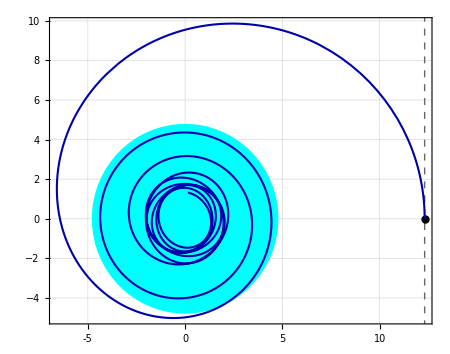

```mathematica
ThesisOrbitPlot[{rbarNumIn[t] Cos[phiNumIn[t]],rbarNumIn[t] Sin[phiNumIn[t]]},{t,t0,tFinish},rbarStar,"Fig_Orbit_With_r0","\\bar{r}(t)\\cos(\\phi(t))",(*Keeping default labels*)"\\bar{r}(t)\\sin(\\phi(t))",rbar0 (*This is your rbar0 value*)]
```

```mathematica
rbarStar // N
```

4.75852

```mathematica
rbarNumInTVIIB = rbarNumIn
```

InterpolatingFunction[…]

Saved Radial Plot: /home/em/Documents/thesis/neutron_star/Radial_Evolution_Plot.pdf

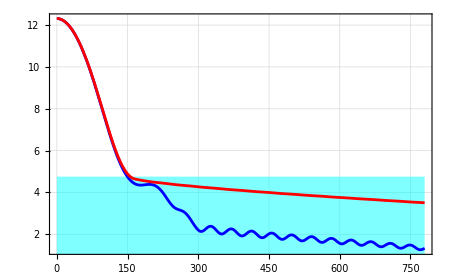

```mathematica
ThesisStandardPlotRadial[{rbarNumInTVIIB[t], rbarNumIn[t]},(*The function to plot*){t,0, 780},(*The variable and range*)"Radial_Evolution_Plot",(*The output PDF filename*)"\\bar{r}(t)",(*y-axis MaTeX label*)"t",(*x-axis MaTeX label*){"\\large{\\textbf{Improved TVII}}","\\large{\\textbf{Constant Density}}"},(*Legend label*)rbarStar              (*The height of the cyan shaded region*)]
```

```mathematica
Part[NearSubsonicTime[[1]], 2]
```

3.54499

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_Mach_Number_Evolution.pdf

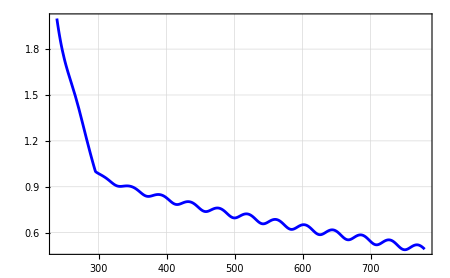

```mathematica
ThesisStandardPlot[Mach[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],{t,NearSubsonicTime[[1,1]], tFinish},"Fig_Mach_Number_Evolution","\\mathcal{M}(t)","t" ]
```

```mathematica
massNumInTVII = massNumIn
```

InterpolatingFunction[…]

```mathematica
massNumInInf = massNumIn
```

InterpolatingFunction[{{0, 1597.18301593193001794272720127}}, <>]

```mathematica
constDensityDirectory="/home/em/Documents/thesis/constant_density";
```

```mathematica
Get[FileNameJoin[constDensityDirectory, "constStarSim_Final.mx"]]
```

Saved Time Plot: /home/em/Documents/thesis/neutron_star/Fig_mass_growth_change_mdot_Final.pdf

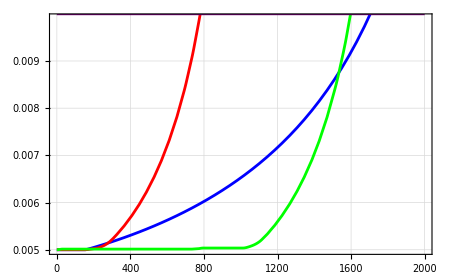

```mathematica
Show[ThesisStandardPlotTime[{massNumIn[t], massNumInTVII[t], massNumInInf[t], 10^-2},{t,0,2000},"Fig_mass_growth_change_mdot_Final","m(t)","t"], PlotRange->{Automatic, {5 10^-3, 0.0099}}]
```

## Gravitational-wave strains

### h_+

```mathematica
hplusInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFuncInside[r] Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hplusOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hplusInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_Gravitational_Wave_Plus.pdf

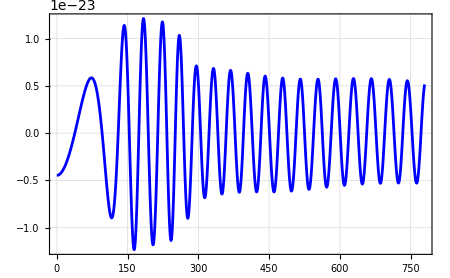

```mathematica
ThesisStandardPlot[hplusFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]],{t,0,tFinish},"Fig_Gravitational_Wave_Plus","h_{+}(t)","t"] (*10^8 it gets jagged*)
```

### h_x

```mathematica
hxInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFuncInside[r] Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hxOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hxInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_Gravitational_Wave_Polarisations.pdf

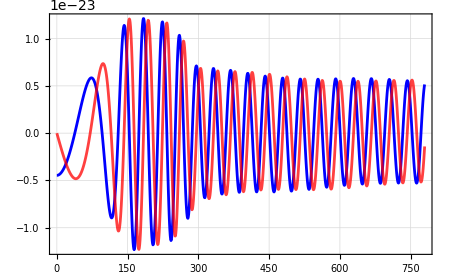

```mathematica
ThesisStandardPlotPOL[{hplusFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]], hxFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]]},{t,0,tFinish},"Fig_Gravitational_Wave_Polarisations","h_+(t), \\text{ } h_{\\times}(t)","t",{},(*No labels for a single curve*)None,(*No special xTick*)1000,(*pPoints:High initial sampling for fast oscillations*)60       (*wPrec:High precision to resolve 10^-23 amplitudes*)](*10^8 it gets jagged*)
```

```mathematica
hplus[t_]:= hplusFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]] 
hcross[t_]:= hxFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]]
```

```mathematica
hNorm[t_] := Abs[hplusFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]] - I*hxFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]]]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_Strain_Dashed_Final.pdf

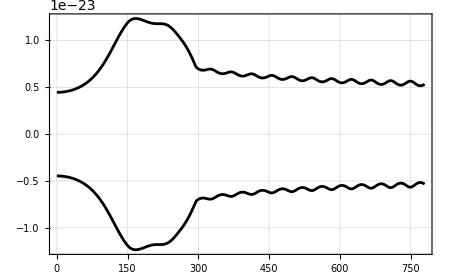

```mathematica
ThesisStandardPlot[{hNorm[t],-hNorm[t]},{t,0,tFinish},"Fig_Strain_Dashed_Final","h(t)","t",{},None,500,(*High sampling for waves*)30,(*High precision*){Directive[Black],(*hNorm top*)Directive[Black]    (*hNorm bottom*)}]
```

```mathematica
hData=Table[hplus[t]-I*hcross[t],{t,0, tFinish,0.1}];
dt=0.1;
fs=1/dt;
n=Length[hData];
tM=6.89589*10^-6; (*SI conversion for 1.4 M_sun*)

ftData=Fourier[hData,FourierParameters->{1,-1}];

(*This line is the fix:it scales the axis to Hz*)
frequencies=Table[((i-1)*fs/n)/tM,{i,1,Floor[n/2]+1}];

powerSpectrum=Abs[ftData[[1;;Length[frequencies]]]]^2;
peakIndex=First[Ordering[powerSpectrum,-1]];
prominentFrequency=frequencies[[peakIndex]];

Print["The most prominent GW frequency is (Hz): ",prominentFrequency];
```

The most prominent GW frequency is (Hz): 0.

```mathematica
hData = Table[hplus[t] - I*hcross[t], {t, 300, .9tFinish, 0.5}];
```

```mathematica
dt=0.5; 
fs=1/dt; (*Sampling frequency*)
n=Length[hData];
```

```mathematica
(*Compute the FT*)ftData=Fourier[hData,FourierParameters->{1,-1}];

(*Calculate the corresponding frequency bins*)
frequencies=Table[(i-1)*fs/(n) / (tM),{i,1,Floor[n/2]+1}];
powerSpectrum=Abs[ftData[[1;;Length[frequencies]]]]^2;
```

```mathematica
(*Find the index of the peak*)
peakIndex=First[Ordering[powerSpectrum,-1]];

(*Extract the actual frequency value*)
prominentFrequency=frequencies[[peakIndex]];

Print["The most prominent GW frequency is: ",prominentFrequency];
```

The most prominent GW frequency is: 360.731

Saved Linear Spectrum: /home/em/Documents/thesis/neutron_star/Fig_GW_Spectrum_Linear.pdf

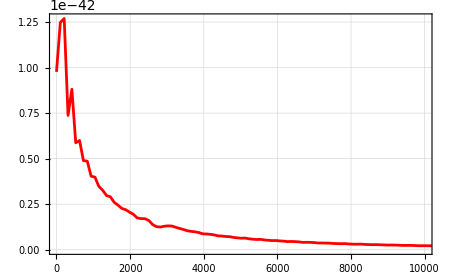

```mathematica
ThesisListPlot[Transpose[{frequencies,powerSpectrum}],"Fig_GW_Spectrum_Linear","Power","f \\text{ (Hz)}" ]
```

```mathematica
hData=Table[hplus[t]-I*hcross[t],{t,0, tFinish,0.1}];
dt=0.1;
fs=1/dt;
n=Length[hData];
tM=6.89589*10^-6; (*SI conversion for 1.4 M_sun*)

ftData=Fourier[hData,FourierParameters->{1,-1}];

(*This line is the fix:it scales the axis to Hz*)
frequencies=Table[((i-1)*fs/n)/tM,{i,1,Floor[n/2]+1}];

powerSpectrum=Abs[ftData[[1;;Length[frequencies]]]]^2;
peakIndex=First[Ordering[powerSpectrum,-1]];
prominentFrequency=frequencies[[peakIndex]];

Print["The most prominent GW frequency is (Hz): ",prominentFrequency];
```

The most prominent GW frequency is (Hz): 90.7926

Saved Linear Spectrum: /home/em/Documents/thesis/neutron_star/Fig_GW_Spectrum_Linear_FULL_BOUND.pdf

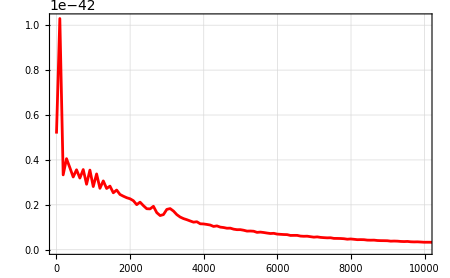

```mathematica
ThesisListPlot[Transpose[{frequencies,powerSpectrum}],"Fig_GW_Spectrum_Linear_FULL_BOUND","Power","f \\text{ (Hz)}" ]
```

```mathematica
Get[FileNameJoin[exportDirectory, "ns_borb_freqs_snrWeighted.mx"]]
snrWeighted;
```

```mathematica
{tMin,tMax}={Max[data[[1,1]],dataET[[1,1]]],Min[data[[-1,1]],dataET[[-1,1]]]};
```

```mathematica
(*1. Filter out 0 or negative frequencies for the log-interpolation*)
snrDataFiltered=Select[Transpose[{frequencies,snrWeighted}],#[[1]]>0&];
funcSNR=Interpolation[snrDataFiltered];

(*2. Define the exact bounds of the SNR data*)
{snrFMin,snrFMax}={Min[snrDataFiltered[[All,1]]],Max[snrDataFiltered[[All,1]]]};
```

Saved Matched Log-Log: /home/em/Documents/thesis/neutron_star/Fig_BOUND_ns_LIGO_ET.pdf

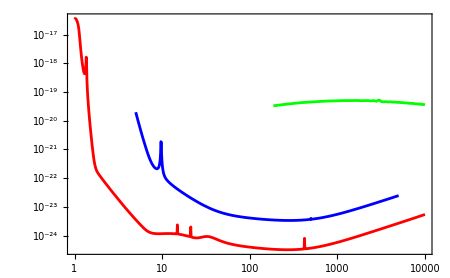

```mathematica
ThesisStandardLogLogPlot[{(*LIGO*)If[data[[1,1]]<=f<=data[[-1,1]],funcData[f],Indeterminate],(*ET*)If[dataET[[1,1]]<=f<=dataET[[-1,1]],funcDataET[f],Indeterminate],(*SNR-restricted to its specific frequency range up to 10,000*)If[snrFMin<=f<=snrFMax,funcSNR[f],Indeterminate]},{f,0.00000001,10000},(*The total x-axis range*)"Fig_BOUND_ns_LIGO_ET","h_c(f)","f \\text{ [Hz]}",{}]
```

Saved Matched Log-Log: /home/em/Documents/thesis/neutron_star/Fig_BOUND_ns_LIGO_LISA_ET.pdf

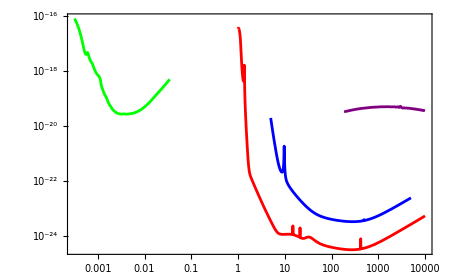

```mathematica
ThesisStandardLogLogPlot[{(*LIGO*)If[data[[1,1]]<=f<=data[[-1,1]],funcData[f],Indeterminate],(*ET*)If[dataET[[1,1]]<=f<=dataET[[-1,1]],funcDataET[f],Indeterminate],If[dataLISA[[1,1]]<=f<=dataLISA[[-1,1]],LISA[f],Indeterminate],(*SNR-restricted to its specific frequency range up to 10,000*)If[snrFMin<=f<=snrFMax,funcSNR[f],Indeterminate]},{f,0.00000001,10000},(*The total x-axis range*)"Fig_BOUND_ns_LIGO_LISA_ET","h_c(f)","f \\text{ [Hz]}",{}]
```

## Capturing the PBH from infinity

Assuming PBH comes from infinity and just hits in and enters the star

#### Approaching the problem differently, using Keplerian orbits on the outside of the star and then GR on the inside to reduce the stiffness of the problem causing the error in the solver.

Setting v_inf to something physical is essential, most dark matter comes from the galactic halo, where things move at roughly 200km/s so with setting c = 1, vinf should be 6.67 x 10^-4 which implies the Energy at infinity should be approximately equal to 1 and very little energy loss is needed to bound the orbit.

### Defining Initial Data Functions

```mathematica
vinf = 6.67 10^-4;
```

```mathematica
(*rbar0 = 15.67;*)
```

```mathematica
InitialEnergyAtInfinity[vinf_] := 1/(√(1 - vinf^2)); (*eq47 2404 paper*)
```

```mathematica
(*general formula for the magnitude of the velocity, for a general spherically symmetric Isotropic metric*)
umagVel[ur_, uphi_, rbar_] := √(ur^2 + (uphi/rbar)^2)
umagE[Energy_, rbar_] := A[rbar] √((Energy/α[rbar])^2 - 1); (*eq 48 in paper*)
```

```mathematica
(*Defining the Impact angle, which is the angle between the radial vector and the PBH's velocity vector*) (*It is the angle the PBH enters the star*)

urInit[psi_, Einit_] := -umagE[Einit , rbarStar]Cos[psi];
uphiInit[psi_, rbarStar_, Einit_] := rbarStar umagE[Einit ]Sin[psi]; (*Is defining angular momentum, L is equal to this*)
```

### Setting the Initial conditions

```mathematica
(*we start at rbarStar*)
phi0 = 0;
Einf = InitialEnergyAtInfinity[vinf]//N
 u = umagE[Einf, rbarStar];
ImpactAngle = .85Pi/2; (*In radians, measured from center of star to the position of particle, in unit circle fashion, (*1.5 Pi/4 η = 10^3 is nice*)pi/2 corresponds to grazing the star as it enters and 0 corresponds to a radial drop*)
ur0 = -u*Cos[ImpactAngle]
AngularMomentumUphi0 = (rbarStar)(u) Sin[ImpactAngle]
```

1.

-0.206519

4.09335

### Sanity Check to see if the two energy formulas match up

```mathematica
alphaaa //N
```

1.4739

```mathematica
Einf = InitialEnergyAtInfinity[vinf] //N
α[rbarStar]^2  Ut[rbarStar, ur0, AngularMomentumUphi0] //N (*This Ut was upper indexed*)
```

1.

1.

### Performing the integration

```mathematica
(*WhenEvent[rbar[t] < rbarStar && Mach[rbar[t], ur[t], uphi[t]] < 2, AppendTo[NearSubsonicTime, {t, rbar[t]}]]*)
```

```mathematica
(*,
Method->{"DiscontinuityProcessing"->False}*)
```

```mathematica
t0=0;
tEnd=140000;
m=0.005;
(*Reset currentTime and currentR*)currentTime=t0;
currentR=(999/1000) rbarStar;

Monitor[solIn=NDSolve[{rbar'[t]==Piecewise[{{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}}],ur'[t]==Piecewise[{{durdt2DOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},{durdt2DInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}}],uphi'[t]==Piecewise[{{duphidtOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}}],phi'[t]==Piecewise[{{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}}],mass'[t]==Piecewise[{{0,rbar[t]>=rbarStar},{mdot[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}}],rbar[t0]==(999/1000) rbarStar,ur[t0]==ur0,phi[t0]==0,uphi[t0]==AngularMomentumUphi0,mass[t0]==m,WhenEvent[rbar[t]<=10^-2,"StopIntegration"],WhenEvent[mass[t]>=0.01,"StopIntegration"]},{rbar,ur,phi,uphi,mass},{t,t0,tEnd},MaxSteps->Infinity,WorkingPrecision->30,StepMonitor:>(currentTime=t;currentR=rbar[t])][[1]],(*The[[1]] stays inside the Monitor*)(*This is the UI that Monitor displays*)Dynamic[Column[{Row[{"Progress: ",ProgressIndicator[currentTime,{t0,tEnd}]}],Row[{"Current Time: ",NumberForm[currentTime,{8,2}]," / ",tEnd}],Row[{"Current radial coord: ",NumberForm[currentR,{6,10}]}]},Spacings->1.5]]]
```

NDSolve::precw: The precision of the differential equation ({<<616793328 bytes>>}) is less than WorkingPrecision (30.).

InterpolatingFunction::dmval: Input value {4.76872454381963675116296183756} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{rbar→InterpolatingFunction[{{0, 1597.18301593193001794272720127}}, <>],ur→InterpolatingFunction[{{0, 1597.18301593193001794272720127}}, <>],phi→InterpolatingFunction[{{0, 1597.18301593193001794272720127}}, <>],uphi→InterpolatingFunction[{{0, 1597.18301593193001794272720127}}, <>],mass→InterpolatingFunction[{{0, 1597.18301593193001794272720127}}, <>]}

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,100,10,tFinish}]
```

1597.18301593193001794272720127

30.9217

```mathematica
(*Bundle your solutions and constants into a list*)dataToSave={rbarNumIn,urNumIn,phiNumIn,uphiNumIn,massNumIn,tFinish,tSurface};

(*Export using DumpSave-Note:DumpSave requires a Symbol or a list of Symbols*)
DumpSave[FileNameJoin[{exportDirectory,"NeutronStarSimInf_Final.mx"}],{rbarNumIn,urNumIn,phiNumIn,uphiNumIn,massNumIn,tFinish,tSurface}];

Print[Style["Binary .mx file saved. Load speed: Instant.",Green,Bold]];
```

Binary .mx file saved. Load speed: Instant.

```mathematica
(*Load the file*)Get[FileNameJoin[{exportDirectory,"NeutronStarSimInf_Final.mx"}]];
```

Saved Orbit: /home/em/Documents/thesis/neutron_star/Fig_Orbit_With_r0_inf.pdf

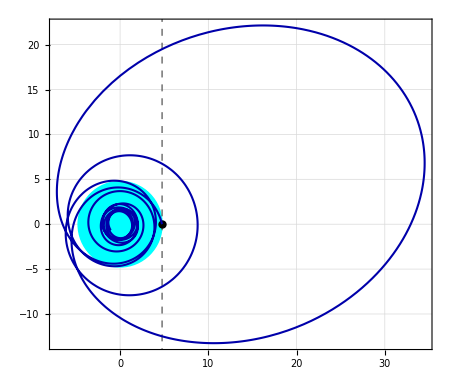

```mathematica
ThesisOrbitPlot[{rbarNumIn[t] Cos[phiNumIn[t]],rbarNumIn[t] Sin[phiNumIn[t]]},{t,t0,tFinish},rbarStar,"Fig_Orbit_With_r0_inf","\\bar{r}(t)\\cos(\\phi(t))",(*Keeping default labels*)"\\bar{r}(t)\\sin(\\phi(t))",rbarStar (*This is your rbar0 value*)]
```

Saved: /home/em/Documents/thesis/neutron_star/Fig_Mach_Number_Evolution_inf.pdf

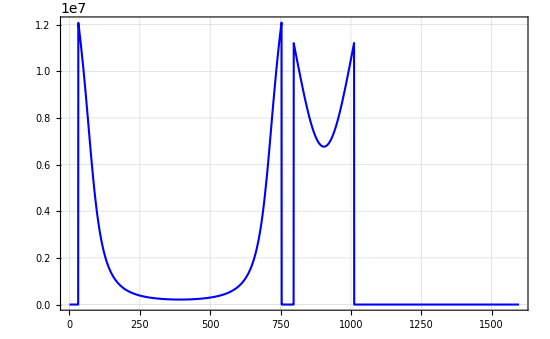

```mathematica
ThesisStandardPlot[Mach[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],{t,0, tFinish},"Fig_Mach_Number_Evolution_inf","\\mathcal{M}(t)","t"]
```

```mathematica
hplus[t_]:= hplusFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]] 
hcross[t_]:= hxFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]]
```

```mathematica
hNorm[t_] := Abs[hplusFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]] - I*hxFull[3 10^20, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t],phiNumIn[t]]]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_Strain_Dashed_Final_Inf.pdf

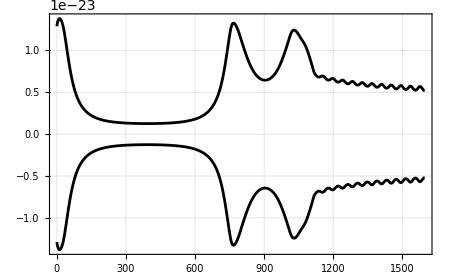

```mathematica
ThesisStandardPlot[{hNorm[t],-hNorm[t]},{t,0,tFinish},"Fig_Strain_Dashed_Final_Inf","h(t)","t",{},None,500,(*High sampling for waves*)30,(*High precision*){Directive[Black],(*hNorm top*)Directive[Black]    (*hNorm bottom*)}]
```

## Stuff

## Gravitational-wave strains

### h_+

```mathematica
hplusInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFuncInside[r] Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hplusOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hplusInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_Gravitational_Wave_Plus_inf.pdf

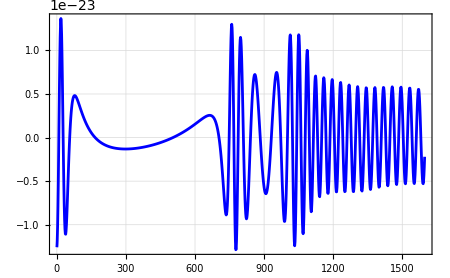

```mathematica
ThesisStandardPlot[hplusFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]],{t,0,tFinish},"Fig_Gravitational_Wave_Plus_inf","h_{+}(t)","t"]
```

### h_x

```mathematica
hxInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFuncInside[r] Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hxOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hxInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

Saved Standard (High-Precision): /home/em/Documents/thesis/neutron_star/Fig_Gravitational_Wave_Polarisations_inf.pdf

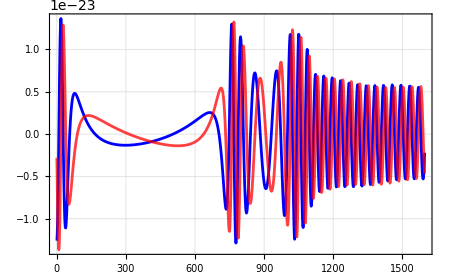

```mathematica
ThesisStandardPlotPOL[{hplusFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]], hxFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]]},{t,0,tFinish},"Fig_Gravitational_Wave_Polarisations_inf","h_+(t), \\text{ } h_{\\times}(t)","t",{},(*No labels for a single curve*)None,(*No special xTick*)1000,(*pPoints:High initial sampling for fast oscillations*)60       (*wPrec:High precision to resolve 10^-23 amplitudes*)]
```

```mathematica
hData = Table[hplus[t] - I*hcross[t], {t, 0, .9tFinish, 0.1}];
```

```mathematica
(*Ensure your time step dt is defined based on your data generation*)dt=0.1; (*Example value;replace with your actual time step*)
fs=1/dt; (*Sampling frequency*)
n=Length[hData];
```

```mathematica
(*Compute the DFT*)ftData=Fourier[hData,FourierParameters->{1,-1}];

(*Calculate the corresponding frequency bins*)
(*Only the first half of the data is needed for physical frequencies (Nyquist)*)
frequencies=Table[(i-1)*fs/(n*tM),{i,1,Floor[n/2]+1}];
powerSpectrum=Abs[ftData[[1;;Length[frequencies]]]]^2;
```

```mathematica
(*Find the index of the peak*)peakIndex=First[Ordering[powerSpectrum,-1]];

(*Extract the actual frequency value*)
prominentFrequency=frequencies[[peakIndex]];

Print["The most prominent GW frequency is: ",prominentFrequency];
```

The most prominent GW frequency is: 100.879

Saved Linear Spectrum: /home/em/Documents/thesis/neutron_star/Fig_GW_Spectrum_Linear_inf_Full.pdf

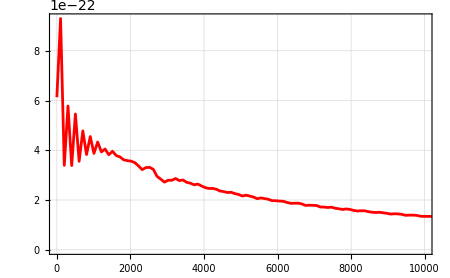

```mathematica
ThesisListPlot[Transpose[{frequencies,sqrtFT}],"Fig_GW_Spectrum_Linear_inf_Full","Power","f \\text{ (Hz)}" (*Zooming to the first 1000 Hz to see peaks*)]
```

```mathematica
ThesisLogLogPlot[data_,fileName_String,yLabel_:"Power",xLabel_:"Frequency (Hz)"]:=Module[{finalPlot,fullPath},finalPlot=ListLogLogPlot[(*Ensure data is treated as a single list of {x,y} pairs*)Flatten[{data},0],Joined->True,(*Forces a line instead of just points*)Frame->True,Axes->False,PlotStyle->{Red,AbsoluteThickness[$ThesisThickness]},FrameStyle->$FrameStyle,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->Automatic,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,(*Set PlotRange to All to see the whole dataset accurately*)PlotRange->{{1, 10000}, All},PlotRangePadding->Scaled[0.02]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Log-Log Spectrum: ",Red,Bold],fullPath];
finalPlot]
```

```mathematica
sqrtFT = Sqrt[powerSpectrum];
```

Saved Log-Log Spectrum: /home/em/Documents/thesis/neutron_star/Fig_GW_Spectrum_LogLog_Full_sqrt.pdf

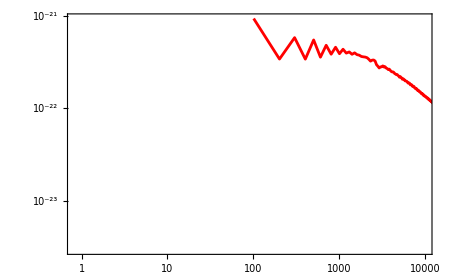

```mathematica
ThesisLogLogPlot[Transpose[{frequencies,sqrtFT}],"Fig_GW_Spectrum_LogLog_Full_sqrt","\\text{Strain Amplitude [Hz]}^{-\\frac{1}{2}}","f \\text{ [Hz]}"]
```

```mathematica
snrWeigthed = sqrtFT*2*Sqrt[frequencies];
```

Saved Log-Log Spectrum: /home/em/Documents/thesis/neutron_star/Fig_GW_Spectrum_LogLog_Full_sqrt_SNR.pdf

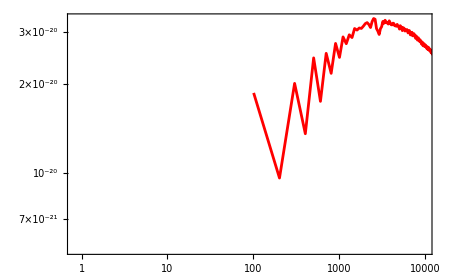

```mathematica
ThesisLogLogPlot[Transpose[{frequencies,snrWeigthed}],"Fig_GW_Spectrum_LogLog_Full_sqrt_SNR","h_c(f)","f \\text{ [Hz]}"]
```

```mathematica
dataLISA = Import[FileNameJoin[ exportDirectory, "LISA.csv"]];
```

```mathematica
(*This opens a window to let you pick the file manually*)(*ET*)
path=SystemDialogInput["FileOpen"];
```

```mathematica
dataET = Cases[Import[path, "Table"], {__?NumberQ}];
```

```mathematica
(*1. Import and extract only the rows that contain numbers*) (*LIGO*)data=Cases[Import["https://dcc.ligo.org/public/0149/T1800044/005/aLIGODesign.txt","Table"],{__?NumberQ}];
```

```mathematica
funcData=Interpolation[data];
funcDataET=Interpolation[dataET];
LISA = Interpolation[dataLISA];
```

```mathematica
{tMin,tMax}={Max[data[[1,1]],dataET[[1,1]]],Min[data[[-1,1]],dataET[[-1,1]]]};
```

Saved Matched Log-Log: /home/em/Documents/thesis/neutron_star/MyGWPlot_Comparison.pdf

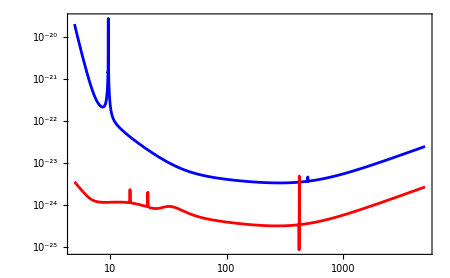

```mathematica
ThesisStandardLogLogPlot[{funcData[t],funcDataET[t]},{t,tMin,tMax},"MyGWPlot_Comparison","h_c(f)","f [Hz]",{"\\large{\\textbf{LIGO}}","\\large{\\textbf{ET}}"}]
```

```mathematica
{tMin,tMax}={Max[dataLISA[[1,1]]],Min[dataLISA[[-1,1]]]};
```

Saved Matched Log-Log: /home/em/Documents/thesis/neutron_star/LISA.pdf

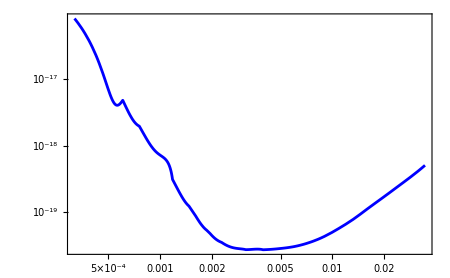

```mathematica
ThesisStandardLogLogPlot[{LISA[t]},{t,tMin,tMax},"LISA","h_c(f)","f [Hz]",{"\\large{\\textbf{LISA}}"}]
```

```mathematica
Get[FileNameJoin[exportDirectory, "inf_frequencies_snrWeighted.mx"]]
snrWeighted;
```

```mathematica
{tMin,tMax}={Max[data[[1,1]],dataET[[1,1]]],Min[data[[-1,1]],dataET[[-1,1]]]};
```

```mathematica
(*1. Filter out 0 or negative frequencies for the log-interpolation*)
snrDataFiltered=Select[Transpose[{frequencies,snrWeighted}],#[[1]]>0&];
funcSNR=Interpolation[snrDataFiltered];

(*2. Define the exact bounds of the SNR data*)
{snrFMin,snrFMax}={Min[snrDataFiltered[[All,1]]],Max[snrDataFiltered[[All,1]]]};
```

Saved Matched Log-Log: /home/em/Documents/thesis/neutron_star/Fig_INF_ns_LIGO_ET.pdf

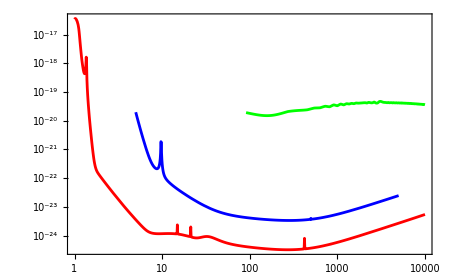

```mathematica
ThesisStandardLogLogPlot[{(*LIGO*)If[data[[1,1]]<=f<=data[[-1,1]],funcData[f],Indeterminate],(*ET*)If[dataET[[1,1]]<=f<=dataET[[-1,1]],funcDataET[f],Indeterminate],(*SNR-restricted to its specific frequency range up to 10,000*)If[snrFMin<=f<=snrFMax,funcSNR[f],Indeterminate]},{f,0.00000001,10000},(*The total x-axis range*)"Fig_INF_ns_LIGO_ET","h_c(f)","f \\text{ [Hz]}",{}]
```

Saved Matched Log-Log: /home/em/Documents/thesis/neutron_star/Fig_INF_LISA_ns_Full_Spectrum.pdf

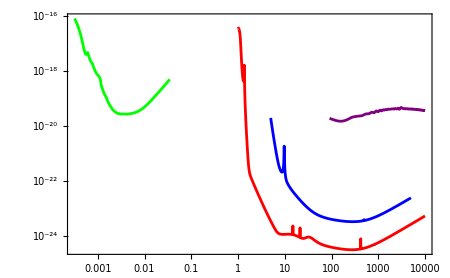

```mathematica
ThesisStandardLogLogPlot[{(*1. LIGO*)If[data[[1,1]]<=f<=data[[-1,1]],funcData[f],Indeterminate],(*2. ET*)If[dataET[[1,1]]<=f<=dataET[[-1,1]],funcDataET[f],Indeterminate],(*3. LISA*)If[dataLISA[[1,1]]<=f<=dataLISA[[-1,1]],LISA[f],Indeterminate],(*4. SNR*)If[snrFMin<=f<=snrFMax,funcSNR[f],Indeterminate]},{f,0.00000001,10000},"Fig_INF_LISA_ns_Full_Spectrum","h_c(f)","f \\text{ [Hz]}",{}]
```

```mathematica
DumpSave[FileNameJoin[{exportDirectory,"inf_FT.mx"}],{funcSNR}];
```

```mathematica
ThesisStandardLogLogPlot[funcs_,range_,fileName_String,yLabel_,xLabel_,labels_List]:=Module[{finalPlot,fullPath},finalPlot=LogLogPlot[funcs,range,Frame->True,Axes->False,(*Red=LIGO,Blue=ET,Green=LISA,Orange=SNR*)PlotStyle->({#,AbsoluteThickness[$ThesisThickness]}&/@{Red,Blue,Darker[Green],Orange}),FrameStyle->$FrameStyle,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->Automatic,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},PlotLegends->Placed[LineLegend[MaTeX/@labels,LegendStyle->Directive[FontSize->$ThesisFontSize]],{0.15,0.2} (*Placed bottom-left to avoid covering curves*)],ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,(*Force the X-axis from 10^-3 to 10^4*)PlotRange->{{0.00000001,10000},All},PlotRangePadding->Scaled[0.02]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Full Spectrum: ",Red,Bold],fullPath];
finalPlot]
```